# Lattice Plane Densities

## Setup

```mathematica
<<Notation`
```

```mathematica
<<LatticePlane`
```

```mathematica
Symbolize[Subscript[_, _]]
```

```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\epdo"];
```

## Tests

## Al

```mathematica
mpid="mp-134";
n=1;
hklMax=3;
dFactor=0.1;(*Angstroms*)
```

```mathematica
{t,{Subscript[𝒜, int,n],Subscript[𝒜, int,ct],Subscript[hkl, list],Subscript[𝒜, full,n],Subscript[𝒜, full,ct],Subscript[hkl, full],Subscript[ℰ, unique]}}=AbsoluteTiming@DensityHKL[mpid,n,hklMax,"Method"->"PDF"];Print@t
```

```mathematica
{Subscript[hkl, list],reflectionList,pg}=PlotSetup[mpid];
PlotSymmetrizedFullHKL[Subscript[𝒜, int,n],Subscript[hkl, list],pg,Subscript[ℰ, unique],"∫"]
```

-Graphics3D- | -Graphics3D-

```mathematica
{t,{Subscript[𝒜, b,n],Subscript[𝒜, b,ct],Subscript[hkl, list],Subscript[𝒜, full,n],Subscript[𝒜, full,ct],Subscript[hkl, full],Subscript[ℰ, unique]}}=AbsoluteTiming@DensityHKL[mpid,n,hklMax,dFactor,"Method"->"HardSphere"];Print@t
```

3.74663

```mathematica
{Subscript[hkl, list],reflectionList,pg}=PlotSetup[mpid,n,hklMax];
PlotSymmetrizedFullHKL[Subscript[𝒜, b,n],Subscript[hkl, list],pg,Subscript[ℰ, unique],"ball"]
```

-Graphics3D- | -Graphics3D-

```mathematica
CrystalPlot[mpid<>"_2",AtomRadiusType->"AtomicRadius"]
```

-Graphics3D-

### Fe_3 C

```mathematica
mpid="mp-510623";
```

```mathematica
{t,{Subscript[𝒜, int,n],Subscript[hkl, list],Subscript[ℰ, unique]}}=AbsoluteTiming@DensityHKL[mpid,"Method"->"PDF"];Print@t
```

450.107

```mathematica
{Subscript[hkl, list],reflectionList,pg}=PlotSetup[mpid];
PlotSymmetrizedFullHKL[Subscript[𝒜, int,n],Subscript[hkl, list],pg,Subscript[ℰ, unique],"∫"]
```

```mathematica
{{-Graphics3D-, -Graphics3D-}, {-Graphics3D-, -Graphics3D-}}
```

```mathematica
{t,{Subscript[𝒜, b,n],Subscript[𝒜, b,ct],Subscript[hkl, list],Subscript[𝒜, full,n],Subscript[𝒜, full,ct],Subscript[hkl, full],Subscript[ℰ, unique]}}=AbsoluteTiming@DensityHKL[mpid,n,hklMax,dFactor,"Method"->"HardSphere"];Print@t
```

10.7586

```mathematica
{Subscript[hkl, list],reflectionList,pg}=PlotSetup[mpid,n,hklMax];
PlotSymmetrizedFullHKL[Subscript[𝒜, b,n],Subscript[hkl, list],pg,Subscript[ℰ, unique],"ball"]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
CrystalPlot[mpid<>"_2"]
(*Show[CrystalPlot[mpid<>"_2"],Graphics3D@{Opacity[0.5],BoundingRegion@Join[Sequence@@Subscript[𝒻, list]]}]*)
```

-Graphics3D-

## Verifying Lattice Planes and Some Setup

```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\epdo\\cif\\stable_elastic"];
crystalData=ImportCrystalData2["mp-134.cif"];(*mp-134, mp-510623, mp-46*)
crystalData=ExpandCrystal2[crystalData,"NewLabel"->"AlCif2"];(*Defaults to 1x1x1*)
{ℰ,𝒻tmp}=(Values/@crystalData⟦"AtomData",;;,{"Element","FractionalCoordinates"}⟧)ᵀ
{a,b,c,α,β,γ}=QUC@Values@crystalData["LatticeParameters"];
{a,b,c}={a,b,c}*1*^10;
(*𝒻=# {a,b,c}&/@𝒻*)
pg=crystalData⟦"SpaceGroup"⟧;
latticeParameters=Values@crystalData⟦"LatticeParameters"⟧;
R=GetCrystalMetric[latticeParameters,ToCartesian->True];
𝒻=𝒻tmp.R
```

{{Al,Al,Al,Al,Al,Al,Al,Al,Al,Al,Al,Al,Al,Al},{{0.,0.,0.},{0.5,0.5,0.},{0.,0.5,0.5},{0.5,0.,0.5},{0.,0.,1.},{0.5,0.5,1.},{0.,1.,0.},{0.5,1.,0.5},{0.,1.,1.},{1.,0.,0.},{1.,0.5,0.5},{1.,0.,1.},{1.,1.,0.},{1.,1.,1.}}}

{{0.,0.,0.},{2.01947,2.01947,0.},{0.,2.01947,2.01947},{2.01947,0.,2.01947},{0.,0.,4.03893},{2.01947,2.01947,4.03893},{0.,4.03893,0.},{2.01947,4.03893,2.01947},{0.,4.03893,4.03893},{4.03893,0.,0.},{4.03893,2.01947,2.01947},{4.03893,0.,4.03893},{4.03893,4.03893,0.},{4.03893,4.03893,4.03893}}

```mathematica
𝒫=MillerToPlane[{-2,3,0},R];
𝒰=RationalUnitCell[R];
ℛ=PlaneIntersection[𝒫,𝒰];
```

```mathematica
Graphics3D[{
{PointSize@Large,MapThread[Text[#1,#2,Background->Opacity[0.5,White],BaseStyle->Medium]&,{{"p1","p2","p3","{0,0,0}"},{Sequence@@𝒫⟦1⟧,{0,0,0}}}]},
{FaceForm[Blue],Opacity[0.25],𝒰},
{Red,𝒫}
},PlotRange->All,Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Subscript[r, Al]=QUC@ElementData["Al","AtomicRadius"];
r=0.05ReplaceAll[ℰ,"Al"->Subscript[r, Al]]*1*^10
(*r=ConstantArray[0.01,Length@ℰ];*)
```

{0.059,0.059,0.059,0.059,0.059,0.059,0.059,0.059,0.059,0.059,0.059,0.059,0.059,0.059}

```mathematica
𝒟=MapThread[MultinormalDistribution[#1,DiagonalMatrix@ConstantArray[#2,3]]&,{𝒻,r}];
```

```mathematica
ℳ=MixtureDistribution[ConstantArray[1,Length@𝒻],𝒟];
```

```mathematica
{Subscript[x, max],Subscript[y, max],Subscript[z, max]}=Max/@(𝒻ᵀ);
```

```mathematica
Subscript[pdf, max]=Max[PDF[ℳ,#]&/@𝒻];
```

```mathematica
Subscript[g, 1]=DensityPlot3D[PDF[ℳ,{x,y,z}],{x,y,z}∈𝒰,PlotRangePadding->0.1,PlotRange->{0 Subscript[pdf, max],Subscript[pdf, max]},PlotPoints->20,BoxRatios->Automatic,PlotLegends->Automatic,OpacityFunction->Interval[{0.1 Subscript[pdf, max],Subscript[pdf, max]}],OpacityFunctionScaling->False];
```

```mathematica
Show[Subscript[g, 1],Graphics3D@{FaceForm[None],𝒰}]
```

-Graphics3D-

```mathematica
Integrate[PDF[ℳ,{x,y,z}],{x,y,z}∈ℛ]
```

0.323016

```mathematica
Subscript[𝒰, tot]=Integrate[PDF[ℳ,{x,y,z}],{x,y,z}∈BoundaryDiscretizeRegion@𝒰]
```

0.125

```mathematica
Subscript[pdf, max2]=Max[PDF[𝒟⟦1⟧,#]&/@𝒻];
Show[DensityPlot3D[PDF[𝒟⟦1⟧,{x,y,z}],{x,-0.1 Subscript[x, max],1.1 Subscript[x, max]},{y,-0.1 Subscript[y, max],1.1 Subscript[y, max]},{z,-0.1 Subscript[z, max],1.1 Subscript[z, max]},PlotRange->{0 Subscript[pdf, max2],Subscript[pdf, max2]},PlotPoints->50,BoxRatios->Automatic,PlotLegends->Automatic,OpacityFunction->Interval[{0.45 Subscript[pdf, max2],0.55 Subscript[pdf, max2]}],OpacityFunctionScaling->False],ListPointPlot3D[𝒻,PlotStyle->{Red,Large}]]
```

-Graphics3D-

```mathematica
(*Show[DensityPlot3D[PDF[𝒟⟦1⟧,{x,y,z}],{x,-0.1 Subscript[x, max],1.1 Subscript[x, max]},{y,-0.1 Subscript[y, max],1.1 Subscript[y, max]},{z,-0.1 Subscript[z, max],1.1 Subscript[z, max]},PlotRange->{0.75 Subscript[pdf, max],1.25 Subscript[pdf, max]},PlotPoints->30,BoxRatios->Automatic,PlotLegends->Automatic,OpacityFunction->Interval[{0.965 Subscript[pdf, max],Subscript[pdf, max]}],OpacityFunctionScaling->False],ListPointPlot3D[𝒻,PlotStyle->{RGBColor[1, 0, 0],Large}]];*)
```

```mathematica
Show[SliceContourPlot3D[PDF[ℳ,{x,y,z}],{"XStackedPlanes",7},{x,y,z}∈𝒰(*{x,0,Subscript[x, max]},{y,0,Subscript[y, max]},{z,0,Subscript[z, max]}*),PlotLegends->Automatic,Contours->20],ListPointPlot3D[𝒻]]
```

-Graphics3D-

```mathematica
ExportCrystalData["DISCUS","AlCif2","AlCif2.txt"]
```

AlCif2.txt

```mathematica
max=3;
Subscript[hkl, list]=MergeSymmetryEquivalentReflections[pg,ReflectionList@max];
```

```mathematica
max=3;
Subscript[hkl, list2]=DeleteCases[ReflectionList@max,{0,0,0}];
npts=Length@Subscript[hkl, list2];
```

```mathematica
Subscript[𝒫, sym]=MillerToPlane[#,R]&/@Subscript[hkl, list];
```

```mathematica
Subscript[ℛ, sym]=PlaneIntersection[Subscript[𝒫, sym],𝒰];
```

```mathematica
Subscript[𝒜, sym]=Area/@PlaneIntersection[Subscript[𝒫, sym],𝒰];
```

```mathematica
(*Clear[x,y,z]
Subscript[ℛ, pdf]=NIntegrate[PDF[ℳ,{x,y,z}],{x,y,z}∈#,AccuracyGoal->10]&/@(*(RegionIntersection[𝒰,#]&/@Subscript[𝒫, sym])*)Subscript[ℛ, sym];*)
```

```mathematica
mPlanes=Show[Graphics3D[{EdgeForm[None],Opacity[0.5],Subscript[ℛ, sym]},BoxRatios->Automatic,Axes->True,PlotRangePadding->0.1],ListPointPlot3D[𝒻,PlotStyle->Red]]
```

-Graphics3D-

```mathematica
vals=Subscript[ℛ, pdf]/Subscript[𝒜, sym];(*Subscript[𝒰, tot]*)
c=ColorData[{"AvocadoColors",{0,Max@vals}}];
Show[Legended[Graphics3D[{PointSize[0.05],Point[Subscript[hkl, list],VertexColors->c/@vals]},Axes->True,BoxRatios->Automatic,AxesLabel->{"h","k","l"},PlotRange->ConstantArray[{0,max},3]],BarLegend[{c,c⟦3⟧},LegendLabel->"ℛ_pdf/𝒜_sym(Å^-2)"]],Graphics3D@{FaceForm[None],ConvexHullMesh@Subscript[hkl, list]}]
```

-Graphics3D-

```mathematica
𝓇=ReflectionList@max;
pi=PositionIndex[ToStandardSetting["m-3m",#]&/@𝓇];(*degenerate sets*)
Subscript[vals, replace]=Thread[Keys@PositionIndex[Subscript[hkl, list]]->vals]/.pi;
n=Length/@Keys@Subscript[vals, replace];
Subscript[vals, 2]=Range@npts/.(Thread[Keys@#->Values@#]&/@Subscript[vals, replace]//Flatten);
{Subscript[hkl, list,sub],Subscript[vals, sub]}=DeleteCases[{Subscript[hkl, list2],Subscript[vals, 2]}ᵀ,{{x_,y_,z_},_}/;AllTrue[Thread[{x,y,z}>0],TrueQ]]ᵀ;
```

```mathematica
Show[Legended[Graphics3D[{Opacity[1],PointSize[0.08],Point[Subscript[hkl, list,sub],VertexColors->c/@Subscript[vals, sub]]},Axes->True,BoxRatios->Automatic,AxesLabel->{"h","k","l"},ViewPoint->{Back,Right,Top},AxesEdge->{{1,-1},{1,-1},{1,-1}}, PlotRange->ConstantArray[{-max,max},3]],BarLegend[{c,c⟦3⟧},LegendLabel->"ℛ_pdf/𝒜(Å^-2)"]]]
```

-Graphics3D-

```mathematica
Subscript[𝒫, sym2]=MillerToPlane[#,R]&/@Subscript[hkl, list2];
```

```mathematica
Subscript[ℛ, sym2]=PlaneIntersection[Subscript[𝒫, sym2],𝒰];
```

```mathematica
mPlanes2=Show[Graphics3D[{EdgeForm[None],Opacity[0.5],Subscript[ℛ, sym2]},BoxRatios->Automatic,Axes->True,PlotRangePadding->0.1],ListPointPlot3D[𝒻,PlotStyle->Red]]
```

-Graphics3D-

```mathematica
(*mPlanes2=Graphics3D[{EdgeForm[None],Opacity[0.5],Subscript[ℛ, sym2]},BoxRatios->Automatic,Axes->True]*)
```

```mathematica
TableForm[{{mPlanes,mPlanes2}}]
```

-Graphics3D- | -Graphics3D-

```mathematica
Length/@{Subscript[hkl, list],Subscript[hkl, list2]}
```

{34,728}

```mathematica
ExpandCrystal["AlCif",{3,3,3},"NewLabel"->"AlCif3"];(*Defaults to 1x1x1*)
{Subscript[ℰ, 2],Subscript[𝒻tmp, 2]}=(Values/@$CrystalData⟦"AlCif3","AtomData",;;,{"Element","FractionalCoordinates"}⟧)ᵀ;
Subscript[R, 2]=GetCrystalMetric["AlCif3",ToCartesian->True];
Subscript[𝒻, 2]=Subscript[𝒻tmp, 2].Subscript[R, 2];
Subscript[𝒻, 2]=#-1(Subscript[R, 2]⟦1⟧+Subscript[R, 2]⟦2⟧+Subscript[R, 2]⟦3⟧)&/@Subscript[𝒻, 2];
Subscript[𝒰, 2]=RationalUnitCell[Subscript[𝒻, 2]];
(*Subscript[𝒰, 2,p]=(*DiscretizeRegion@*)(*CanonicalizePolyhedron@*)ConvexHullMesh@Rationalize[Subscript[𝒻, 2],0];*)
MeshCoordinates@ConvexHullMesh@Subscript[𝒻, 2];
```

```mathematica
Subscript[r, 2]=0.3ReplaceAll[Subscript[ℰ, 2],"Al"->Subscript[r, Al]]*1*^10;
Subscript[𝒟, 2]=MapThread[MultinormalDistribution[#1,DiagonalMatrix@ConstantArray[#2,3]]&,{Subscript[𝒻, 2],Subscript[r, 2]}];
Subscript[ℳ, 2]=MixtureDistribution[ConstantArray[1,Length@Subscript[𝒻, 2]],Subscript[𝒟, 2]];
```

```mathematica
Subscript[ℛ, 2]=PlaneIntersection[Subscript[𝒫, sym],Subscript[𝒰, 2]];
```

```mathematica
Subscript[hkl, list]
```

{{0,0,1},{0,0,2},{0,1,1},{0,0,3},{0,1,2},{1,1,1},{0,0,4},{0,1,3},{0,2,2},{1,1,2},{0,1,4},{0,2,3},{1,1,3},{1,2,2},{0,2,4},{0,3,3},{1,1,4},{1,2,3},{2,2,2},{0,3,4},{1,2,4},{1,3,3},{2,2,3},{0,4,4},{1,3,4},{2,2,4},{2,3,3},{1,4,4},{2,3,4},{3,3,3},{2,4,4},{3,3,4},{3,4,4},{4,4,4}}

```mathematica
Animate[Show[ListPointPlot3D[Subscript[𝒻, 2],BoxRatios->Automatic],Graphics3D@{{FaceForm[None],𝒰,ConvexHullMesh@Subscript[𝒻, 2]},{FaceForm[Red],Opacity[0.5],Subscript[ℛ, sym]⟦pgnum⟧,Subscript[ℛ, 2]⟦pgnum⟧}},ImageSize->Small],{pgnum,Range@Length@Subscript[hkl, list]}];
```

```mathematica
(*Clear[x,y,z]
SetOptions[LinearSolve,Method->Automatic(*"DivisionFreeRowReduction"*)];*)
```

```mathematica
(*Clear[PolygonBallsIntersection]
PolygonBallsIntersection[P_,c_,r_]:=Total[Table[Area@RegionIntersection[i,Ball[j⟦1⟧,j⟦2⟧]],{i,MeshPrimitives[DiscretizeRegion@P,2]},{j,{c,r}ᵀ}]/.Undefined->0]*)
```

```mathematica
{Subscript[t, b],Subscript[ℐ, b]}=AbsoluteTiming@Parallelize[PolygonBallsIntersection[#,Subscript[𝒻, 2],Subscript[r, 2]]&/@Subscript[ℛ, 2]];Print@Subscript[t, b]
```

13.0539

```mathematica
Subscript[𝒜, b]=Total[Subscript[ℐ, b],{2}]
```

{78.249,78.2334,78.2946,52.7734,71.5384,113.141,41.901,62.9665,65.1945,74.841,64.0996,71.661,52.1926,70.3185,71.5439,71.426,66.7292,66.9223,4.7415,65.6346,68.122,66.8359,65.3571,74.424,63.032,69.1537,63.8572,61.5122,63.2151,57.6893,66.3635,50.7465,60.7988,72.2065}

```mathematica
Subscript[ℛ, pdf2]=Integrate[PDF[Subscript[ℳ, 2],{x,y,z}],{x,y,z}∈#]&/@Subscript[ℛ, tmp](*(RegionIntersection[Subscript[𝒰, 2],#]&/@Subscript[𝒫, sym])*)
(*Subscript[ℛ, pdf2]=Integrate[PDF[Subscript[ℳ, 2],{x,y,z}],{x,y,z}∈RegionIntersection[Subscript[𝒰, 2],Subscript[𝒫, sym]⟦-1⟧]]*)
```

{1.73358×10^-6}

```mathematica
NIntegrate[PDF[Subscript[ℳ, 2],{x,y,z}],{x,y,z}∈Subscript[ℛ, 2]⟦1⟧,AccuracyGoal->10]
```

General::munfl: 0.0257587 1.37220155304×10^-1321 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0257587 1.79904794463×10^-1141 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.129305 and 4.5836×10^-6 for the integral and error estimates.

0.129305

```mathematica
{t_∫,ℐ_∫}=AbsoluteTiming@ProbabilityIntersection[Subscript[𝒟, 2],Subscript[ℛ, 2]];Print@t_∫
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

46.4301

```mathematica
Subscript[𝒜, int]=Mean@ℐ_∫;
```

```mathematica
Subscript[𝒜, sym2]=Area@Subscript[ℛ, 2];
```

```mathematica
Subscript[vals, int]=Subscript[𝒜, int]/Subscript[𝒜, sym2];
c=ColorData[{"AvocadoColors",{0,Max@Subscript[vals, int]}}];
Show[Legended[Graphics3D[{PointSize[0.05],Point[Subscript[hkl, list],VertexColors->c/@Subscript[vals, int]]},Axes->True,BoxRatios->Automatic,AxesLabel->{"h","k","l"},PlotRange->ConstantArray[{0,max},3]],BarLegend[{c,c⟦3⟧},LegendLabel->"ℛ_pdf/𝒜_sym(Å^-2)"]],Graphics3D@{FaceForm[None],ConvexHullMesh@Subscript[hkl, list]}]
```

-Graphics3D-

```mathematica
Subscript[vals, replace]=Thread[Keys@PositionIndex[Subscript[hkl, list]]->Subscript[vals, int]]/.pi;
n=Length/@Keys@Subscript[vals, replace];
Subscript[vals, 2]=Range@npts/.(Thread[Keys@#->Values@#]&/@Subscript[vals, replace]//Flatten);
{Subscript[hkl, list,sub],Subscript[vals, sub]}=DeleteCases[{Subscript[hkl, list2],Subscript[vals, 2]}ᵀ,{{x_,y_,z_},_}/;AllTrue[Thread[{x,y,z}>0],TrueQ]]ᵀ;
```

```mathematica
c=ColorData[{"AvocadoColors",{0(*Min@Subscript[vals, int]*),Max@Subscript[vals, int]}}];
Show[Legended[Graphics3D[{Opacity[0.25],PointSize[0.08],Point[Subscript[hkl, list,sub],VertexColors->c/@Subscript[vals, sub]]},Axes->True,BoxRatios->Automatic,AxesLabel->{"h","k","l"},ViewPoint->{Back,Right,Top},AxesEdge->{{1,-1},{1,-1},{1,-1}}, PlotRange->ConstantArray[{-max,max},3]],BarLegend[{c,c⟦3⟧},LegendLabel->"𝒜_int/𝒜(Å^-2)"]]]
```

-Graphics3D-

```mathematica
{Subscript[𝒜, b,n],Subscript[𝒜, int,n]}=#/Subscript[𝒜, sym2]&/@{Subscript[𝒜, b],Subscript[𝒜, int]};
```

```mathematica
c=ColorData[{"AvocadoColors",{0,Max@Subscript[𝒜, b,n]}}];
Show[Legended[Graphics3D[{PointSize[0.05],Point[Subscript[hkl, list],VertexColors->c/@Subscript[𝒜, b,n]]},Axes->True,BoxRatios->Automatic,AxesLabel->{"h","k","l"},PlotRange->ConstantArray[{0,max},3]],BarLegend[{c,c⟦3⟧},LegendLabel->"𝒜_b/𝒜(Å^-2)"]],Graphics3D@{FaceForm[None],ConvexHullMesh@Subscript[hkl, list]}]
```

-Graphics3D-

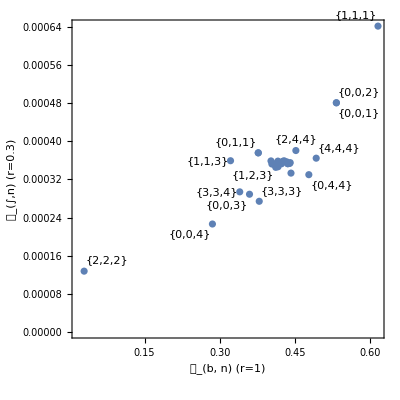

```mathematica
ListPlot[MapThread[(*Tooltip*)Labeled[{#1,#2},#3]&,{Subscript[𝒜, b,n],Subscript[𝒜, int,n],Subscript[hkl, list]}],Frame->True,FrameLabel->{"𝒜_(b, n)","𝒜_(∫,n)"},AspectRatio->1,PlotRange->All]
```

I probably need to use NIntegrate instead, though it’s slower. Maybe not super slow if I set AccuracyGoal→10. Actually seems to be faster than hard sphere model.

```mathematica
TeXport["tmp","∫_({x, y, z} ∈ ℛ) Prⅆ𝒜",{},Print->True,Export->False]
```

# Code Graveyard

```mathematica
(*<<LatticePlane` (*calculate various lattice plane quantities via package I wrote -- lost package without backup..*)*)
```

```mathematica
(*?"LatticePlane`*"*)
```

```mathematica
(*pad[δ_][{min_,max_}]:={min,max}+δ(max-min){-1,1}

VoronoiCells[pts_]/;MatrixQ[pts,NumericQ]&&2≤Last[Dimensions[pts]]≤3:=Block[{bds,dm,conn,adj,lc,pc,cpts,hpts,hns,hp,vcells},bds=pad[.1]/@MinMax/@Transpose[pts];
dm=DelaunayMesh[pts];
conn=dm["ConnectivityMatrix"[0,1]];
adj=conn.Transpose[conn];
lc=conn["MatrixColumns"];
pc=adj["MatrixColumns"];
cpts=MeshCoordinates[dm];
vcells=Table[hpts=PropertyValue[{dm,{1,lc[[i]]}},MeshCellCentroid];
hns=Transpose[Transpose[cpts[[DeleteCases[pc[[i]],i]]]]-cpts[[i]]];
hp=MapThread[HalfSpace,{hns,hpts}];
BoundaryDiscretizeGraphics[#,PlotRange->bds]&/@hp,{i,MeshCellCount[dm,0]}];
AssociationThread[cpts,RegionIntersection@@@vcells]]*)
```

```mathematica
(*Show[ListPointPlot3D[𝒻tmp.R,PlotStyle->{Red,Large}],Graphics3D@Arrow[{{0,0,0},#}]&/@R]*)
```

```mathematica
(*{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}=R;
V=Subscript[a, 1].(Subscript[a, 2]×Subscript[a, 3]);
{Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}={Subscript[a, 2]×Subscript[a, 3],Subscript[a, 3]×Subscript[a, 1],Subscript[a, 1]×Subscript[a, 2]}/V*)
```

```mathematica
(*𝒫*)
```

InfinitePlane[{{2.85595,1.42798,1.42798}},{{0.,2.47333,0.824443},{0.,0.,2.33188}}]

```mathematica
(*Simplify/@RegionDistance[𝒫,𝒻⟦1⟧]*)
```

RegionDistance::regp: A correctly specified region expected at position 1 of RegionDistance[InfinitePlane[{{2.85595,1.42798,1.42798}},{{0.,2.47333,0.824443},{0.,0.,2.33188}}],{0.,0.,0.}].

RegionDistance[InfinitePlane[{{2.85595,1.42798,1.42798}},{{0.,2.47333,0.824443},{0.,0.,2.33188}}],{0.,0.,0.}]

```mathematica
(*ElementData["Al",#]&/@{"AtomicRadius","CovalentRadius","VanDerWaalsRadius"}*)
```

{118. pm,121. pm,Missing[NotAvailable]}

```mathematica
(*RegionIntersection[Triangle@Round[PolygonCoordinates@ℛ,$MachineEpsilon],𝒰]*)
```

```mathematica
Subscript[hkl, list]⟦1⟧
```

{4,4,4}

```mathematica
Graphics3D[{Subscript[𝒫, sym]⟦1⟧,𝒰}]
```

-Graphics3D-

```mathematica
(*ℛ=Cases[RegionIntersection[RegionIntersection[𝒫,ℬ],#]&/@MeshPrimitives[MeshRegion@𝒰,3],_Polygon]*)
```

{}

```mathematica
(*LinearSolve[{{-0.28559547900000004,-0.28559547900000004},{0.4755346105499629,-0.14279773950000002},{0.06331304384998765,2.1890795818191617}},{-1.1102230246251565*^-16,-5.551115123125783*^-17,-5.551115123125783*^-17}],*)
```

```mathematica
(*Polygon@DeleteDuplicatesBy[Flatten[ℛ⟦;;,1,1⟧,1],Round[#,100$MachineEpsilon]&]*)
```

Polygon[…]

```mathematica
(*RegionIntersection[RegionIntersection[𝒫,ℬ],#]&/@MeshPrimitives[MeshRegion@𝒰,2]*)
```

{EmptyRegion[3],Point[{{0.,0.,2.33188}}],Point[{{0.,0.,2.33188}}],EmptyRegion[3],EmptyRegion[3],EmptyRegion[3],EmptyRegion[3],EmptyRegion[3],EmptyRegion[3],EmptyRegion[3],EmptyRegion[3],EmptyRegion[3],EmptyRegion[3],Point[{{0.,0.,2.33188}}],Point[{{0.,0.,2.33188}}],Line[{{{0.713989,0.356994,0.356994},{0.,0.,2.33188}}}],Line[{{{0.,0.618332,0.206111},{0.713989,0.356994,0.356994}}}],Line[{{{0.,0.,2.33188},{0.,0.618332,0.206111}}}]}

```mathematica
(*ℛ=Cases[RegionIntersection[RegionIntersection[𝒫,ℬ],#]&/@MeshPrimitives[MeshRegion@𝒰,2],_Line]*)
```

{Line[{{{0.713989,0.356994,0.356994},{0.,0.,2.33188}}}],Line[{{{0.,0.618332,0.206111},{0.713989,0.356994,0.356994}}}],Line[{{{0.,0.,2.33188},{0.,0.618332,0.206111}}}]}

```mathematica
(*Polygon@DeleteDuplicates[Flatten[ℛ⟦;;,1,1⟧,1],Round[#1,100$MachineEpsilon]==Round[#2,100$MachineEpsilon]&]*)
```

Polygon[…]

```mathematica
(*SeedRandom[1];n=10;
pts=Table[RandomReal[{-1,1},{3}],{n}];
ptsc=Map[{#,RandomReal[]}&,pts]*)
```

{{{0.634779,-0.777161,0.579052},0.472565},{{-0.624394,-0.517278,-0.868522},0.807161},{{0.0844932,-0.537691,-0.207988},0.0118355},{{0.400948,-0.576348,0.497314},0.316876},{{-0.154299,-0.50501,0.954344},0.789804},{{0.650326,0.85055,0.156112},0.011978},{{-0.414261,-0.583898,0.160949},0.391276},{{-0.742358,-0.387145,0.424024},0.458902},{{-0.218836,0.639934,-0.349297},0.458845},{{0.18652,0.0375483,-0.661974},0.727517}}

```mathematica
(*{ColorData["TemperatureMap"][#2],Point[#1]}&@@@ptsc*)
```

{{RGBColor[0.968227217868299, 0.975824491626109, 0.9386672118669253],Point[{0.634779,-0.777161,0.579052}]},{RGBColor[0.9204757450303185, 0.7224198594719111, 0.2548711216584602],Point[{-0.624394,-0.517278,-0.868522}]},{RGBColor[0.19736461534022126, 0.32477310273490406, 0.9345509949176181],Point[{0.0844932,-0.537691,-0.207988}]},{RGBColor[0.7849053573600884, 0.8318932977621426, 0.9791956887302069],Point[{0.400948,-0.576348,0.497314}]},{RGBColor[0.9312513863836227, 0.7651416866681452, 0.2635414556281399],Point[{-0.154299,-0.50501,0.954344}]},{RGBColor[0.19758667286567558, 0.32500649927341685, 0.934563640765188],Point[{0.650326,0.85055,0.156112}]},{RGBColor[0.9004425696207522, 0.923452479425896, 0.9903662101966404],Point[{-0.414261,-0.583898,0.160949}]},{RGBColor[0.960276518857803, 0.9698948733221558, 0.9521256714172845],Point[{-0.742358,-0.387145,0.424024}]},{RGBColor[0.9602431789086133, 0.9698700084426394, 0.9521821072548112],Point[{-0.218836,0.639934,-0.349297}]},{RGBColor[0.9658214396620548, 0.8963698318518214, 0.3217231764769662],Point[{0.18652,0.0375483,-0.661974}]}}

```mathematica
(*Graphics3D[Point[Subscript[hkl, list],VertexColors->(Hue/@Rescale[f[##]&@@@Subscript[hkl, list]])],Axes->True,AxesLabel->{x,y,z}]*)
```

```mathematica
(*Graphics3D[{PointSize[0.03],{ColorData["TemperatureMap"][#2],Point[#1]}&@@@ptsc},Axes->True]*)
```

$Aborted

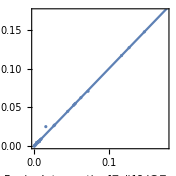

```mathematica
Show[ListPlot[{{0.008667801198469901,0.007370455760750967,0.006644844516609633,0.0069230144184923995,0.0625973283212835,0.0047836581504950865,0.003902904156697402,0.005375046850998238,0.044892115830191266,0.0023255987577125293,0.005719388219237289,0.026302933311578285,0.055125325675401425,0.14785791547467877,0.02726867623939715,0.0020940548528406676,0.0015144048113787203,0.004220943426131787,0.015439980883343906,0.0005223426744065592,0.005228346969247854,0.008957450187961794,0.05397654554516405,0.12739933021387964,0.003111900066302223,0.000023158434174822394,0.006177699804349747,0.000945871966322791,0.05273316834255076,0.11720134209294703,0.00005641549265737101,0.07221300450608323,0.19460125097049413,0.2683614944836945},{0.008667801198469834,0.00733427676270593,0.006644844516609645,0.005809330187732485,0.06259732832128354,0.004783658150495084,0.0040773639399022624,0.005375046850998213,0.04489211583019144,0.0025053558930553045,0.005719388219237245,0.026302933311578333,0.05512532567540218,0.14785791547467866,0.027268676239397084,0.0020940548528406715,0.0015144048113787177,0.004220943426131676,0.0251121824661324,0.0005337684636298643,0.0052283469692478365,0.008957450187961786,0.05397654554516462,0.12739933021387903,0.004672536976754979,0.000023158434174822435,0.0061776998043496,0.0009458719663227973,0.05273316834255148,0.11720134209294644,0.00005641549265737053,0.0709539623106574,0.19460125097049283,0.2683614944836946}}ᵀ,AspectRatio->1,ImageSize->Medium,Frame->True,FrameLabel->{"RegionIntersection[𝒰,#]&/@𝒫_sym","ℛ_sym"}],Plot[x,{x,0,1}]]
```

```mathematica
(*ListPointPlot3D[List/@Subscript[hkl, list],PlotStyle->({PointSize[Large],Blend[{{400,Darker[Green]},{600,Yellow},{800,Red}},#1]}&/@Flatten@Subscript[ℛ, pdf])]*)
```

```mathematica
(*AllTrue[Sequence@@Thread[Subscript[hkl, list2]⟦1⟧>0]]*)
```

```mathematica
(*KeyDrop[PositionIndex[Subscript[hkl, list2]],;*)
```

```mathematica
(*{Subscript[hkl, list,sub],Subscript[vals, sub]}=Select[{Subscript[hkl, list2],Subscript[vals, 2]}ᵀ,AnyTrue[#⟦1⟧,#⟦1⟧≤0&]&]ᵀ*)
```

```mathematica
(*AllTrue[#⟦1⟧,#⟦1⟧>0&]&/@{{Subscript[hkl, list2]⟦1⟧,Subscript[vals, 2]⟦1⟧}}
AllTrue[Subscript[hkl, list2]⟦1⟧>0//Thread,TrueQ]
{Subscript[hkl, list,sub],Subscript[vals, sub]}=DeleteCases[{Subscript[hkl, list2],Subscript[vals, sub]}ᵀ,{{x_,y_,z_},_}/;AllTrue[Thread[{x,y,z}>0],TrueQ]]ᵀ;*)
```

```mathematica
(*{Subscript[hkl, list,sub],Subscript[vals, sub]}=Cases[{Subscript[hkl, list2],Subscript[vals, 2]}ᵀ,Select[Subscript[hkl, list2],AnyTrue[#⟦1⟧,#⟦1⟧≤0&,TrueQ]&]]ᵀ;*)
```

```mathematica
(*,ListPointPlot3D[𝒻,PlotStyle->{Red,Large}]*)
```

```mathematica
(*MultinormalDistribution[𝒻⟦1⟧,DiagonalMatrix[ConstantArray[r⟦1⟧,3]]]*)
```

MultinormalDistribution[{0.,0.,0.},{{0.059,0.,0.},{0.,0.059,0.},{0.,0.,0.059}}]

```mathematica
(*pad[δ_][{min_,max_}]:={min,max}+δ(max-min){-1,1}

VoronoiCells[pts_]/;MatrixQ[pts,NumericQ]&&2≤Last[Dimensions[pts]]≤3:=Block[{bds,dm,conn,adj,lc,pc,cpts,hpts,hns,hp,vcells},bds=pad[.1]/@MinMax/@Transpose[pts];
dm=DelaunayMesh[pts];
conn=dm["ConnectivityMatrix"[0,1]];
adj=conn.Transpose[conn];
lc=conn["MatrixColumns"];
pc=adj["MatrixColumns"];
cpts=MeshCoordinates[dm];
vcells=Table[hpts=PropertyValue[{dm,{1,lc[[i]]}},MeshCellCentroid];
hns=Transpose[Transpose[cpts[[DeleteCases[pc[[i]],i]]]]-cpts[[i]]];
hp=MapThread[HalfSpace,{hns,hpts}];
BoundaryDiscretizeGraphics[#,PlotRange->bds]&/@hp,{i,MeshCellCount[dm,0]}];
AssociationThread[cpts,RegionIntersection@@@vcells]]*)
```

```mathematica
(*𝒱=VoronoiCells[Subscript[𝒻, 2]];*)
```

```mathematica
(*Show[MapIndexed[BoundaryMeshRegion[#,MeshCellStyle->{1->Black,2->{Opacity[0.5],ColorData[112][First[#2]]}}]&,Values[𝒱]],Graphics3D[{PointSize[Large],Point[Subscript[𝒻, 2]]}],Method->{"RelieveDPZFighting"->True},ImageSize->Small]*)
```

-Graphics3D-

```mathematica
(*Subscript[pdf, max]=Max[PDF[ℳ,#]&/@𝒻];*)
```

```mathematica
(*r=ConstantArray[0.01,Length@ℰ];*)
```

```mathematica
(*Integrate[PDF[Subscript[ℳ, 2],{x,y,z}],{x,y,z}∈#]&/@{(RegionIntersection[Subscript[𝒫, sym]⟦1⟧])}*)
```

```mathematica
(*Integrate[PDF[Subscript[ℳ, 2],{x,y,z}],{x,y,z}∈RegionIntersection[Subscript[𝒰, 2],Subscript[𝒫, sym]⟦1⟧]]*)
```

1.73358×10^-6

```mathematica
(*SetOptions[LinearSolve,Method->"DivisionFreeRowReduction"];
LinearSolve[{{0.,2.85595479},{-1.2366647000999258,1.427977395},{0.3650708737397452,1.427977395}},{0.,0.,-1.1102230246251565*^-16}]*)
```

{0.,0.}

```mathematica
(*Area@RegionIntersection[Subscript[ℛ, 2]⟦1⟧,Ball[#,First@Subscript[r, 2]]]&/@Subscript[𝒻, 2]*)
```

```mathematica
(*Subscript[𝒜, sym2]=Area@RegionIntersection[𝒰,Subscript[𝒫, sym]⟦1⟧]*)
```

```mathematica
(*Graphics3D[{Subscript[𝒰, 2],,Subscript[𝒫, sym]⟦1⟧}]*)
```

```mathematica
ImportCrystalData["Al_mp-134_conventional_standard.cif"(*"al.cif"*),"AlCifconventional"]
ImportCrystalData["Al.cif"(*"al.cif"*),"AlCifprimitive"]
```

{FormulaUnits→4,SpaceGroup→P1,LatticeParameters→<|a→4.03893 Å,b→4.03893 Å,c→4.03893 Å,α→90 °,β→90 °,γ→90 °|>,AtomData→{«4»}}

{FormulaUnits→1,SpaceGroup→P1,LatticeParameters→<|a→2.85595 Å,b→2.85595 Å,c→2.85595 Å,α→60 °,β→60 °,γ→60 °|>,AtomData→{«1»}}

```mathematica
ExpandCrystal["AlCifconventional","NewLabel"->"AlCifc"];(*Defaults to 1x1x1*)
{Subscript[ℰ, c],Subscript[𝒻tmp, c]}=(Values/@$CrystalData⟦"AlCifc","AtomData",;;,{"Element","FractionalCoordinates"}⟧)ᵀ
Subscript[R, c]=GetCrystalMetric["AlCifc",ToCartesian->True];
Subscript[𝒻, c]=Subscript[𝒻tmp, c].Subscript[R, c]
```

{{Al,Al,Al,Al,Al,Al,Al,Al,Al,Al,Al,Al,Al,Al},{{0.,0.,0.},{0.,0.,1.},{0.,1.,0.},{0.,1.,1.},{1.,0.,0.},{1.,0.,1.},{1.,1.,0.},{1.,1.,1.},{0.,0.5,0.5},{1.,0.5,0.5},{0.5,0.,0.5},{0.5,1.,0.5},{0.5,0.5,0.},{0.5,0.5,1.}}}

{{0.,0.,0.},{0.,0.,4.03893},{0.,4.03893,0.},{0.,4.03893,4.03893},{4.03893,0.,0.},{4.03893,0.,4.03893},{4.03893,4.03893,0.},{4.03893,4.03893,4.03893},{0.,2.01947,2.01947},{4.03893,2.01947,2.01947},{2.01947,0.,2.01947},{2.01947,4.03893,2.01947},{2.01947,2.01947,0.},{2.01947,2.01947,4.03893}}

```mathematica
ExpandCrystal["AlCifprimitive","NewLabel"->"AlCifp"];(*Defaults to 1x1x1*)
{Subscript[ℰ, p],Subscript[𝒻tmp, p]}=(Values/@$CrystalData⟦"AlCifp","AtomData",;;,{"Element","FractionalCoordinates"}⟧)ᵀ
Subscript[R, p]=GetCrystalMetric["AlCifp",ToCartesian->True];
Subscript[𝒻, p]=Subscript[𝒻tmp, p].Subscript[R, p]
```

{{Al,Al,Al,Al,Al,Al,Al,Al},{{0.,0.,0.},{0.,0.,1.},{0.,1.,0.},{0.,1.,1.},{1.,0.,0.},{1.,0.,1.},{1.,1.,0.},{1.,1.,1.}}}

{{0.,0.,0.},{0.,0.,2.33188},{0.,2.47333,0.824443},{0.,2.47333,3.15632},{2.85595,1.42798,1.42798},{2.85595,1.42798,3.75985},{2.85595,3.90131,2.25242},{2.85595,3.90131,4.5843}}

```mathematica
(*ListPointPlot3D[#,BoxRatios->Automatic,Axes->False]&/@{Subscript[𝒻, c],Subscript[𝒻, p]}*)
```

{-Graphics3D-,-Graphics3D-}

```mathematica
(*FindGeometricTransform[Subscript[𝒻, c],Subscript[𝒻, p]]*)
```

FindGeometricTransform::input: {{0.,0.,0.},{0.,0.,4.03893},{0.,4.03893,0.},{0.,4.03893,4.03893},{4.03893,0.,0.},{4.03893,0.,4.03893},{4.03893,4.03893,0.},{4.03893,4.03893,4.03893},{0.,2.01947,2.01947},{4.03893,2.01947,2.01947},«4»} and {{0.,0.,0.},{0.,0.,2.80064},{0.,2.80064,0.},{0.,2.80064,2.80064},{2.80064,0.,0.},{2.80064,0.,2.80064},{2.80064,2.80064,0.},{2.80064,2.80064,2.80064}} should be images, polygons, lines, points, BSplineCurves, BezierCurves, or commensurate point sets of at least dimension 2.

FindGeometricTransform[{{0.,0.,0.},{0.,0.,4.03893},{0.,4.03893,0.},{0.,4.03893,4.03893},{4.03893,0.,0.},{4.03893,0.,4.03893},{4.03893,4.03893,0.},{4.03893,4.03893,4.03893},{0.,2.01947,2.01947},{4.03893,2.01947,2.01947},{2.01947,0.,2.01947},{2.01947,4.03893,2.01947},{2.01947,2.01947,0.},{2.01947,2.01947,4.03893}},{{0.,0.,0.},{0.,0.,2.80064},{0.,2.80064,0.},{0.,2.80064,2.80064},{2.80064,0.,0.},{2.80064,0.,2.80064},{2.80064,2.80064,0.},{2.80064,2.80064,2.80064}}]

```mathematica
(*SetOptions[LinearSolve,Method->Automatic];
LinearSolve[{{-1.427977395,-1.427977395},{0.5226760025999257,-0.7139886975},{-0.3017671308000247,0.06330374293972052}},{0,0,0}]*)
```

```mathematica
(*{Subscript[𝒜, int]⟦{1,6}⟧,Subscript[𝒜, b]⟦{1,6}⟧,Subscript[𝒜, sym2]⟦{1,6}⟧}*)
```

{{1.09473,0.251143},{0.00140038,0.00132193},{70.2831,53.7725}}

```mathematica
(*BoundaryMeshRegion[Rationalize[MeshCoordinates@Subscript[𝒰, 2,p],0],MeshCells[Subscript[𝒰, 2,p],2]]*)
```

```mathematica
(*Subscript[𝒫, crop]=RegionIntersection[#,BoundingRegion@Subscript[𝒰, 2]]&/@Subscript[𝒫, sym];
Subscript[𝒫, int]=RegionIntersection[#,Subscript[𝒰, 2]]&/@Subscript[𝒫, crop];
shapes=OpenCascadeShape[#]&/@Subscript[𝒫, int];
bmesh=OpenCascadeShapeSurfaceMeshToBoundaryMesh[#]&/@shapes;*)
```

```mathematica
(*Graphics3D@{Polygon@#["Coordinates"]&/@bmesh}*)
```

-Graphics3D-

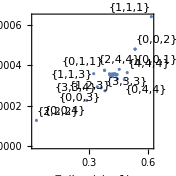

```mathematica
(*ListPlot[MapThread[(*Tooltip*)Labeled[{#1,#2},#3]&,{Subscript[𝒜, b,n],Subscript[𝒜, int,n],Subscript[hkl, list]}],Frame->True,FrameLabel->{"𝒜_(b, n) (r=1)","𝒜_(∫,n) (r=0.3)"},AspectRatio->1,PlotRange->All]*)
```

```mathematica
(*{Subscript[𝒜, b,n],Subscript[𝒜, int,n]}=#/Subscript[𝒜, sym]&/@{Subscript[𝒜, b],Subscript[𝒜, int]};(*normalize by lattice plane area*)*)
```

```mathematica
(*Subscript[𝒜, b,n]=#/Subscript[𝒜, sym]&/@Subscript[𝒜, b];
Subscript[𝒜, int,n]=#/Subscript[𝒜, sym]&/@Subscript[𝒜, int];*)
```

```mathematica
(*ExternalEvaluate["Python",<|"Command"->"numpy.linalg.eigvalsh","Arguments"->{linearMap}|>]*)
```

print(structure_from_cifstr(stableCIFs[1]))

structures = [mg.Structure.from_str( stableCIFs[1]["cif"], fmt="cif" ), mg.Structure.from_str( stableCIFs[1]["cif"], fmt="cif" )]

```mathematica
(*t1=AbsoluteTime[];*)
```

```mathematica
(*t2=AbsoluteTime[];
t2-t1*)
```

1093.673856

[x for x in e_above_hull if x is None]

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

type(e_above_hull[1])

i=1
print(str(i)+' failed')

1 failed

[1,'hello',['a','b']]

jobs[0].result()

```mathematica
{"mineral_prototype","spg_symbol","crystal_system","dimensionality","is_vdw_heterostructure","is_interpenetrated","is_intercalated","is_only_3d","is_only_2d","is_only_1d","is_only_0d","is_3d_2d_1d_0d","is_3d_2d_1d","is_3d_2d_0d","is_3d_1d_0d","is_3d_2d","is_3d_1d","is_3d_0d","is_2d_1d_0d","is_2d_1d","is_2d_0d","is_1d_0d","contains_3d_component","contains_2d_component","contains_1d_component","contains_0d_component","contains_named_molecule","contains_water","contains_oxygen","contains_ammonia","contains_methane","contains_L-shaped","contains_water-like","contains_bent 120 degrees","contains_bent 150 degrees","contains_linear","contains_trigonal planar","contains_trigonal non-coplanar","contains_T-shaped","contains_square co-planar","contains_tetrahedral","contains_rectangular see-saw-like","contains_see-saw-like","contains_trigonal pyramidal","contains_pentagonal planar","contains_square pyramidal","contains_trigonal bipyramidal","contains_hexagonal planar","contains_octahedral","contains_pentagonal pyramidal","contains_hexagonal pyramidal","contains_pentagonal bipyramidal","contains_body-centered cubic","contains_hexagonal bipyramidal","contains_cuboctahedral","contains_distorted_L-shaped","contains_distorted_water-like","contains_distorted_bent 120 degrees","contains_distorted_bent 150 degrees","contains_distorted_linear","contains_distorted_trigonal planar","contains_distorted_trigonal non-coplanar","contains_distorted_T-shaped","contains_distorted_square co-planar","contains_distorted_tetrahedral","contains_distorted_rectangular see-saw-like","contains_distorted_see-saw-like","contains_distorted_trigonal pyramidal","contains_distorted_pentagonal planar","contains_distorted_square pyramidal","contains_distorted_trigonal bipyramidal","contains_distorted_hexagonal planar","contains_distorted_octahedral","contains_distorted_pentagonal pyramidal","contains_distorted_hexagonal pyramidal","contains_distorted_pentagonal bipyramidal","contains_distorted_body-centered cubic","contains_distorted_hexagonal bipyramidal","contains_distorted_cuboctahedral","average_site_cn","average_cation_cn","average_anion_cn","contains_polyhedra","contains_corner_sharing_polyhedra","contains_edge_sharing_polyhedra","contains_face_sharing_polyhedra","contains_corner_tetrahedral","contains_corner_octahedral","contains_corner_trigonal pyramidal","contains_corner_square pyramidal","contains_corner_trigonal bipyramidal","contains_corner_pentagonal pyramidal","contains_corner_hexagonal pyramidal","contains_corner_pentagonal bipyramidal","contains_corner_hexagonal bipyramidal","contains_corner_cuboctahedral","contains_edge_tetrahedral","contains_edge_octahedral","contains_edge_trigonal pyramidal","contains_edge_square pyramidal","contains_edge_trigonal bipyramidal","contains_edge_pentagonal pyramidal","contains_edge_hexagonal pyramidal","contains_edge_pentagonal bipyramidal","contains_edge_hexagonal bipyramidal","contains_edge_cuboctahedral","contains_face_tetrahedral","contains_face_octahedral","contains_face_trigonal pyramidal","contains_face_square pyramidal","contains_face_trigonal bipyramidal","contains_face_pentagonal pyramidal","contains_face_hexagonal pyramidal","contains_face_pentagonal bipyramidal","contains_face_hexagonal bipyramidal","contains_face_cuboctahedral","corner_sharing_octahedral_tilt_angle","frac_site_polyhedra","frac_sites_L-shaped","frac_sites_water-like","frac_sites_bent 120 degrees","frac_sites_bent 150 degrees","frac_sites_linear","frac_sites_trigonal planar","frac_sites_trigonal non-coplanar","frac_sites_T-shaped","frac_sites_square co-planar","frac_sites_tetrahedral","frac_sites_rectangular see-saw-like","frac_sites_see-saw-like","frac_sites_trigonal pyramidal","frac_sites_pentagonal planar","frac_sites_square pyramidal","frac_sites_trigonal bipyramidal","frac_sites_hexagonal planar","frac_sites_octahedral","frac_sites_pentagonal pyramidal","frac_sites_hexagonal pyramidal","frac_sites_pentagonal bipyramidal","frac_sites_body-centered cubic","frac_sites_hexagonal bipyramidal","frac_sites_cuboctahedral","frac_sites_1_coordinate","frac_sites_2_coordinate","frac_sites_3_coordinate","frac_sites_4_coordinate","frac_sites_5_coordinate","frac_sites_6_coordinate","frac_sites_7_coordinate","frac_sites_8_coordinate","frac_sites_9_coordinate","frac_sites_10_coordinate","frac_sites_11_coordinate","frac_sites_12_coordinate","max_bond_length","min_bond_length","average_bond_length"}=={"mineral_prototype","spg_symbol","crystal_system","dimensionality","is_vdw_heterostructure","is_interpenetrated","is_intercalated","is_only_3d","is_only_2d","is_only_1d","is_only_0d","is_3d_2d_1d_0d","is_3d_2d_1d","is_3d_2d_0d","is_3d_1d_0d","is_3d_2d","is_3d_1d","is_3d_0d","is_2d_1d_0d","is_2d_1d","is_2d_0d","is_1d_0d","contains_3d_component","contains_2d_component","contains_1d_component","contains_0d_component","contains_named_molecule","contains_water","contains_oxygen","contains_ammonia","contains_methane","contains_L-shaped","contains_water-like","contains_bent 120 degrees","contains_bent 150 degrees","contains_linear","contains_trigonal planar","contains_trigonal non-coplanar","contains_T-shaped","contains_square co-planar","contains_tetrahedral","contains_rectangular see-saw-like","contains_see-saw-like","contains_trigonal pyramidal","contains_pentagonal planar","contains_square pyramidal","contains_trigonal bipyramidal","contains_hexagonal planar","contains_octahedral","contains_pentagonal pyramidal","contains_hexagonal pyramidal","contains_pentagonal bipyramidal","contains_body-centered cubic","contains_hexagonal bipyramidal","contains_cuboctahedral","contains_distorted_L-shaped","contains_distorted_water-like","contains_distorted_bent 120 degrees","contains_distorted_bent 150 degrees","contains_distorted_linear","contains_distorted_trigonal planar","contains_distorted_trigonal non-coplanar","contains_distorted_T-shaped","contains_distorted_square co-planar","contains_distorted_tetrahedral","contains_distorted_rectangular see-saw-like","contains_distorted_see-saw-like","contains_distorted_trigonal pyramidal","contains_distorted_pentagonal planar","contains_distorted_square pyramidal","contains_distorted_trigonal bipyramidal","contains_distorted_hexagonal planar","contains_distorted_octahedral","contains_distorted_pentagonal pyramidal","contains_distorted_hexagonal pyramidal","contains_distorted_pentagonal bipyramidal","contains_distorted_body-centered cubic","contains_distorted_hexagonal bipyramidal","contains_distorted_cuboctahedral","average_site_cn","average_cation_cn","average_anion_cn","contains_polyhedra","contains_corner_sharing_polyhedra","contains_edge_sharing_polyhedra","contains_face_sharing_polyhedra","contains_corner_tetrahedral","contains_corner_octahedral","contains_corner_trigonal pyramidal","contains_corner_square pyramidal","contains_corner_trigonal bipyramidal","contains_corner_pentagonal pyramidal","contains_corner_hexagonal pyramidal","contains_corner_pentagonal bipyramidal","contains_corner_hexagonal bipyramidal","contains_corner_cuboctahedral","contains_edge_tetrahedral","contains_edge_octahedral","contains_edge_trigonal pyramidal","contains_edge_square pyramidal","contains_edge_trigonal bipyramidal","contains_edge_pentagonal pyramidal","contains_edge_hexagonal pyramidal","contains_edge_pentagonal bipyramidal","contains_edge_hexagonal bipyramidal","contains_edge_cuboctahedral","contains_face_tetrahedral","contains_face_octahedral","contains_face_trigonal pyramidal","contains_face_square pyramidal","contains_face_trigonal bipyramidal","contains_face_pentagonal pyramidal","contains_face_hexagonal pyramidal","contains_face_pentagonal bipyramidal","contains_face_hexagonal bipyramidal","contains_face_cuboctahedral","corner_sharing_octahedral_tilt_angle","frac_site_polyhedra","frac_sites_L-shaped","frac_sites_water-like","frac_sites_bent 120 degrees","frac_sites_bent 150 degrees","frac_sites_linear","frac_sites_trigonal planar","frac_sites_trigonal non-coplanar","frac_sites_T-shaped","frac_sites_square co-planar","frac_sites_tetrahedral","frac_sites_rectangular see-saw-like","frac_sites_see-saw-like","frac_sites_trigonal pyramidal","frac_sites_pentagonal planar","frac_sites_square pyramidal","frac_sites_trigonal bipyramidal","frac_sites_hexagonal planar","frac_sites_octahedral","frac_sites_pentagonal pyramidal","frac_sites_hexagonal pyramidal","frac_sites_pentagonal bipyramidal","frac_sites_body-centered cubic","frac_sites_hexagonal bipyramidal","frac_sites_cuboctahedral","frac_sites_1_coordinate","frac_sites_2_coordinate","frac_sites_3_coordinate","frac_sites_4_coordinate","frac_sites_5_coordinate","frac_sites_6_coordinate","frac_sites_7_coordinate","frac_sites_8_coordinate","frac_sites_9_coordinate","frac_sites_10_coordinate","frac_sites_11_coordinate","frac_sites_12_coordinate","max_bond_length","min_bond_length","average_bond_length"}
```

True

$Aborted

```mathematica
(*mm=MinMax/@(PolygonCoordinates[ℛ⟦1⟧]ᵀ);
Integrate[pdf,{x,mm⟦1,1⟧,mm⟦1,2⟧},{y,mm⟦2,1⟧,mm⟦2,2⟧},{z,mm⟦3,1⟧,mm⟦3,2⟧}]*)
```

$Aborted

```mathematica
(*NIntegrate[PDF[MixtureDistribution[{1,1,1,1},𝒟⟦1,8;;11⟧],{x,y,z}],{x,y,z}∈ℛ⟦1⟧]*4
NIntegrate[PDF[MixtureDistribution[{1,1,1,1,1,1},𝒟⟦1,6;;11⟧],{x,y,z}],{x,y,z}∈ℛ⟦1⟧]*6*)
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

2.05302

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

2.05302

DataFrame([i if isinstance(i,list) else [i] for j in stable_features[0:3] for i in j],axis=0)

import pandas as pd
#[[i if isinstance(i,list) else [i] for i in features] for features in stable_features[0:3]]

```mathematica
(*pi=PositionIndex/@#&/@ids*)
```

```mathematica
(*AssociationMap[Reverse,PositionIndex@𝒟⟦1⟧]*)
```

```mathematica
(*f[i_,j_]:=Thread[#<3j]&/@i
ids=MapThread[f[#1,#2]&,{d,Subscript[r, list]}]*)
```

```mathematica
(*TruePosition[x_]:=Flatten@Position[#,_?TrueQ]&/@x
TruePosition[#]&/@ids*)
```

```mathematica
(*MapThread[{#1ᵀ,#2}ᵀ&,{d⟦1;;1⟧,Subscript[r, list]⟦1;;1⟧}]⟦1⟧*)
```

```mathematica
(*Select[d,#<3Subscript[r, list]⟦1,1⟧&];*)
```

```mathematica
(*Subscript[𝒻, list]=𝒟⟦;;,;;,1⟧;*)
```

```mathematica
(*Subscript[r, list]=𝒟⟦;;,;;,2,1,1⟧⟦;;,1⟧;(*assumes isotropic radius*)*)
```

```mathematica
(*d=RegionDistance[ℛ,#]&/@Subscript[𝒻, list];*)
(*id=Position[d,x_/;x<3 Subscript[r, list]]//Flatten;
𝒟2=𝒟⟦;;,id⟧;*)
```

```mathematica
(*d=Table[RegionDistance[ℛ⟦1⟧,#]&/@Subscript[𝒻, list]⟦1⟧*)
```

```mathematica
(*id=Position[{d,Subscript[r, list]}ᵀ,{x_,y_}/;x<3y]//Flatten;*)
```

```mathematica
(*d=ParallelTable[RegionDistance[i,j],{i,P},{j,Subscript[𝒻, list]}]
id=MapThread[Flatten@Position[{#⟦1⟧,#⟦2⟧}ᵀ,{x_,y_}/;x<3y]&,{d,Subscript[r, list]}]
d=Table[ParallelTable[RegionDistance[i,j],{i,P},{j,k}],{k,Subscript[𝒻, list]}]*)
```

```mathematica
(*𝒟2=MapThread[𝒟⟦#1,#2⟧&,{Range@Length@id,id}]*)
```

```mathematica
(*id=MapThread[Flatten@Position[{#⟦1⟧,#⟦2⟧}ᵀ,{x_,y_}/;x<3y]&,{d,Subscript[r, list]}];
Cases[{{1,1,1},{3,3,3}}ᵀ,{x_,y_}/;x<3y]
Select[{{1,1,1},{3,3,3}}ᵀ,#⟦1⟧<3#⟦2⟧&]*)
```

```mathematica
(*d=ParallelTable[RegionDistance[i,j],{i,P},{j,#}]&/@Subscript[𝒻, list]*)
```

```mathematica
(*NIntegrate[PDF[UniformDistribution[ConstantArray[{1000,1001},3]],{x,y,z}],{x,y,z}∈#]&/@ℛ*)
```

```mathematica
(*ConstantDistribution[m_]:=TransformedDistribution[m,{x,y,z}\[Distributed]MultinormalDistribution[{0,0,0},DiagonalMatrix@ConstantArray[1,3]]]*)
```

```mathematica
(*d=RegionDistance[ℛ⟦1⟧,Subscript[𝒻, list]⟦1⟧];
Length@d
Length@Select[d,#<3Subscript[r, list]⟦1,1⟧&]*)
```

172

25

```mathematica
(*PDF[𝒟⟦1,1⟧,{x,y,z}]//FullSimplify*)
```

(5000 √(5/59) ⅇ^(-500/59 ((403893/100000+x)^2+(403893/100000+y)^2+(403893/100000+z)^2)))/(59 π^(3/2))

```mathematica
(*id=Position[d,x_/;x<Subscript[r, list]⟦1,1⟧]//Flatten
nid=Length@id*)
```

{9,10,23,24,37,38,47,58,59,72,73,86,87,96,107,108,121,122,135,136,145,152,159,166,171}

25

```mathematica
(*ℳ=MixtureDistribution[ConstantArray[1,nid],𝒟⟦1,id⟧];*)
```

```mathematica
(*Total[PDF[#,{x,y,z}]&/@𝒟⟦1⟧]/pdf//Simplify*)
```

$Aborted

```mathematica
(*pdf=PDF[ℳ,{x,y,z}]//Simplify;*)
```

```mathematica
(*(nid/Length@Subscript[𝒻, list]⟦1⟧)NIntegrate[pdf,{x,y,z}∈#]&/@ℛ⟦1;;1⟧//Timing*)
```

{2.15625,{0.171881}}

```mathematica
(*Timing[Total@Table[NIntegrate[PDF[i,{x,y,z}],{x,y,z}∈j(*,AccuracyGoal->10*)]/Length@Subscript[𝒻, list]⟦1⟧,{i,𝒟⟦1⟧},{j,ℛ⟦1;;1⟧}]]*)
```

{8.42188,{0.162332}}

```mathematica
(*d=RegionDistance[P,#]&/@Subscript[𝒻, list];*)
(*id=MapThread[Flatten@Position[{#⟦1⟧,#⟦2⟧}ᵀ,{x_,y_}/;x<3y]&,{d,Subscript[r, list]}];*)
(*ids=Flatten@Position[{#,Subscript[r, list]}ᵀ,{x_,y_}/;x<3y]&/@d;*)
(*id=Position[{#,Subscript[r, list]}ᵀ&,{x_,y_}/;x<3y]//Flatten/@d;*)
```

```mathematica
(*{t_∫,ℐ_∫}=AbsoluteTiming@Table[MapThread[AtomProbabilityIntersection[#1,#2]&,{i,P}],{i,𝒟2}]*)
```

```mathematica
(*{t_∫,ℐ_∫}=AbsoluteTiming[AtomProbabilityIntersection[#,P]&/@𝒟2];*)
(*{t_∫,ℐ_∫}=AbsoluteTiming@Table[AtomProbabilityIntersection[#,P]&/@i,{i,𝒟2}];*)
(*Subscript[𝒜, int]=Mean/@ℐ_∫;*)
```

```mathematica
(*P=ℛ;
Subscript[𝒻, list]=𝒟⟦;;,;;,1⟧;
Subscript[r, list]=𝒟⟦;;,;;,2,1,1⟧⟦;;,1⟧;(*assumes isotropic radius and assumes constant radius for a particular element*)
d=ParallelTable[RegionDistance[i,j],{i,P},{j,#}]&/@Subscript[𝒻, list];
TF=MapThread[DistanceRadiusComparison[#1,#2]&,{d,Subscript[r, list]}];
ids=TruePosition[#]&/@TF;
𝒟2=MapThread[#1/.Thread[Range@Length@#2->#2]&,{ids,𝒟}]/.{}->0;*)
```

```mathematica
(*Join[DiagonalMatrix[ConstantArray[max,3]],{0,0,0}]*)
```

{{max,0,0},{0,max,0},{0,0,max},0,0,0}

```mathematica
(*distances=RegionDistance[#,{x,y,z}]&/@𝒫;*)(*possible speedup in ProbabilityIntersection[]*)
```

```mathematica
(*Show[Graphics3D@{Opacity[0.5],BoundingRegion@Join[Sequence@@Subscript[𝒻, list]]},Graphics3D@{Opacity[0.5],𝒰},Graphics3D@Point[Join[Sequence@@Subscript[𝒻, list]]]]*)
```

-Graphics3D-

```mathematica
(*R=GetCrystalMetric[mpid,ToCartesian->True]*)
```

{{2.62673,-1.31337,0.},{0.,2.27482,0.},{0.,0.,5.20723}}

```mathematica
(*Permutations[DeleteCases[Join[{0},Flatten@R],0.],{3}]*)
```

{{0,5.03018,6.73931},{0,5.03018,4.49085},{0,6.73931,5.03018},{0,6.73931,4.49085},{0,4.49085,5.03018},{0,4.49085,6.73931},{5.03018,0,6.73931},{5.03018,0,4.49085},{5.03018,6.73931,0},{5.03018,6.73931,4.49085},{5.03018,4.49085,0},{5.03018,4.49085,6.73931},{6.73931,0,5.03018},{6.73931,0,4.49085},{6.73931,5.03018,0},{6.73931,5.03018,4.49085},{6.73931,4.49085,0},{6.73931,4.49085,5.03018},{4.49085,0,5.03018},{4.49085,0,6.73931},{4.49085,5.03018,0},{4.49085,5.03018,6.73931},{4.49085,6.73931,0},{4.49085,6.73931,5.03018}}

```mathematica
(*{R1,R2,R3}=R;
𝒪=Floor[n/2](R1+R2+R3)
𝒰pts=#-𝒪&/@{0,R1,R2,R3,R1+R2,R2+R3,R1+R3,R1+R2+R3};
𝒰=ConvexHullMesh@𝒰pts*)
```

```mathematica
(*𝒰=RationalUnitCell[Join[Sequence@@Subscript[𝒻, list]]]*)
```

Polyhedron[…]

$Aborted

```mathematica
(*PolygonBallsIntersection[ℛ,Subscript[𝒻, list],Subscript[r, list]]*)
```

$Aborted

```mathematica
(*AtomPolygonBallsIntersection[ℛ⟦16⟧,Subscript[𝒻, list]⟦1⟧,Subscript[r, list]⟦1⟧]*)
```

{0.803978,0.803978,0.803978,0.803669,0.803669,0.803669,0.803978,0.803978,0.803978,0.811157,0.811157,0.811157,0.811158,0.811158,0.811158,0.811157,0.811157,0.811157}

```mathematica
(*Show[Graphics3D@ℛ⟦16⟧,Graphics3D@{PointSize[Subscript[r, list]⟦1,1⟧/10],Point[Subscript[𝒻, list]⟦1⟧]}]*)
```

-Graphics3D-

```mathematica
(*(*mpid="mp-134";*)
mpid="mp-79";
(*mpid="mp-510623";*)
n=3;
Subscript[hkl, max]=4;*)
```

```mathematica
(*ImportCrystalData[mpid<>".cif"(*Al_mp-134_conventional_standard.cif*)(*"al.cif"*),mpid,"OverwriteWarning"->False];
(*pg=MaterialProperties["mp-134","spacegroup","point_group",1];*)
ExpandCrystal[mpid,{n,n,n},"NewLabel"->mpid<>"_2","StoreTemporarily"->False];(*Defaults to 1x1x1*)*)
```

```mathematica
(*<<MaterialProperties` (*access Materials Project API via package I wrote*)*)
```

```mathematica
(*(*<<CifImport`*)
(*<<MaXrd`*)*)
```

```mathematica
(*SetKey["tMVqZxvIy2DgmwUd"]*)
```

{myKey→tMVqZxvIy2DgmwUd}

```mathematica
(*?MaterialProperties*)
```

```mathematica
(*𝒰=DiscretizeRegion@𝒰;*)
(*ℬ=BoundingRegion[𝒰]*)
(*ℛ=RegionIntersection[𝒫,𝒰];*)
```

```mathematica
(*ElementData["Na",#]&/@{"AtomicRadius","CovalentRadius"}
ElementData["Cl",#]&/@{"AtomicRadius","CovalentRadius"}*)
```

{190. pm,166. pm}

{79. pm,102. pm}

```mathematica
(*Subscript[𝒫, sym2]//DeleteDuplicates//Length
Subscript[hkl, list2]⟦#⟧&/@Select[Values@PositionIndex@Subscript[𝒫, sym2],Length@#≥2&]
{{{0,0,2},{0,0,-2}},{{0,2,0},{0,-2,0}},{{2,0,0},{-2,0,0}}}*)
```

Ok that there are duplicates, see https://www.doitpoms.ac.uk/tlplib/miller_indices/lattice.php